# Input data

```mathematica
FNVHash[data_,old_]:=Module[{prime,hash},
prime=1099511628211;
hash=old;
Do[hash=Mod[BitXor[hash,block]*prime,2^64],{block,data}];
hash
]

DoubleToByte[a_]:=ImportString[ExportString[{a},"Real64"],"Byte"];
IntToByte[a_]:=ImportString[ExportString[{a},"Integer32"],"Byte"];

IdXXZ[L_,D_,J_,Δ_,h_,γ_,μ_,Γ_]:=Module[{hash},
hash=14695981039346656037;

hash=FNVHash[IntToByte[L],hash];
hash=FNVHash[IntToByte[D],hash];
hash=FNVHash[DoubleToByte[J],hash];
hash=FNVHash[DoubleToByte[Δ],hash];
hash=FNVHash[DoubleToByte[h],hash];
hash=FNVHash[DoubleToByte[γ],hash];
hash=FNVHash[DoubleToByte[μ],hash];
hash=FNVHash[DoubleToByte[Γ],hash];

hash
]

XXZData[L_,D_,J_,Δ_,h_,γ_,μ_,Γ_]:=Module[{ID,monitor,Jctrl,Bond,M,Jp,Spec,Corr,X},
SetDirectory[NotebookDirectory[]];
ID=IdXXZ[L,D,J,Δ,h,γ,μ,Γ];

monitor=BinaryReadList["output/open/Monitor_"<>ToString[ID]<>".bin", {"Real64","Real64","Real64"}];
M=BinaryReadList["output/open/M_"<>ToString[ID]<>".bin", "Real64"];
Jp=BinaryReadList["output/open/J_"<>ToString[ID]<>".bin", "Real64"];
Corr=BinaryReadList["output/open/Corr_"<>ToString[ID]<>".bin", "Real64"];
X=BinaryReadList["output/open/Cov_"<>ToString[ID]<>".bin", {"Real64","Real64"}];
Spec=BinaryReadList["output/open/Spectrum_"<>ToString[ID]<>".bin", "Real64"];

Jctrl={monitorᵀ[[1]],monitorᵀ[[2]]}ᵀ;
Bond={monitorᵀ[[1]],monitorᵀ[[3]]}ᵀ;
Corr=ArrayReshape[Corr,{L,L}];
X=Table[X[[i,1]]+I X[[i,2]],{i,Length[X]}];
X=ArrayReshape[X,{2L,2L}];

M=Table[{(i-1)/(L-1),(M[[i]]+1)/2},{i,L}];
Jp=Table[{i,Jp[[i]]},{i,L-1}];

{Jctrl,Bond,M,Jp,Spec,Corr,X}
]

XXZPlots[L_,D_,J_,Δ_,h_,γ_,μ_,Γ_]:=Module[{data,plots,Legends},
plots={};
data=XXZData[L,D,J,Δ,h,γ,μ,Γ];

AppendTo[plots,ListLinePlot[data[[1]],PlotRange->All,AxesLabel->{"t","J_t"},PlotLabel->"Current over time"]];
AppendTo[plots,ListLogLinearPlot[data[[2]],Joined->True,AxesLabel->{"t","Bond"}]];
AppendTo[plots,ListLogPlot[data[[5]],AxesLabel->{"i","σ"},Joined->True,PlotLabel->"Singular Values"]];
AppendTo[plots,ListLinePlot[data[[3]],AxesLabel->{"(i-1)/(L-1)","n"},PlotLabel->"Occupation Profile"]];
AppendTo[plots,ListLinePlot[data[[4]],AxesLabel->{"i","J"},PlotLabel->"Current"]];
AppendTo[plots,MatrixPlot[data[[6]],AxesLabel->{"x","y"},PlotLabel->"Correlation <n n>",PlotLegends->True]];
AppendTo[plots,MatrixPlot[data[[7]]//Re,AxesLabel->{"x","y"},PlotLabel->"Real part of SPA",PlotLegends->True]];
AppendTo[plots,MatrixPlot[data[[7]]//Im,AxesLabel->{"x","y"},PlotLabel->"Imaginary part of SPA",PlotLegends->True]];

ArrayReshape[plots,{2,4}]
]
```

# Results

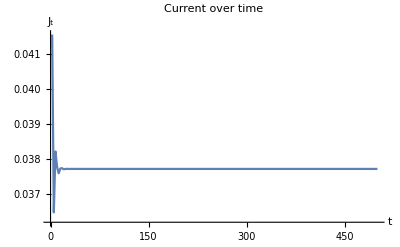
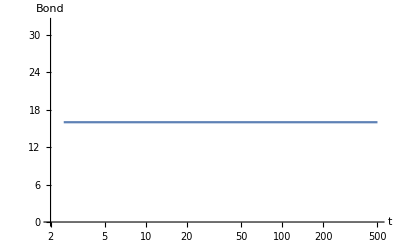
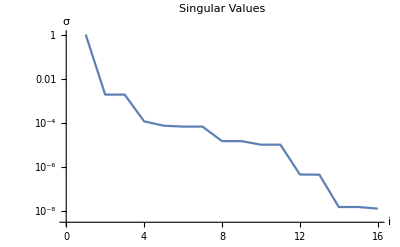
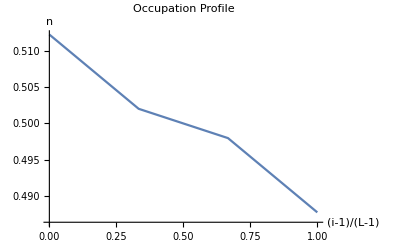
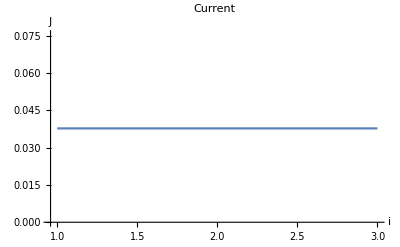
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
XXZPlots[4,16,-0.5,0.25,0.0,0.0,0.1,1.0]
```

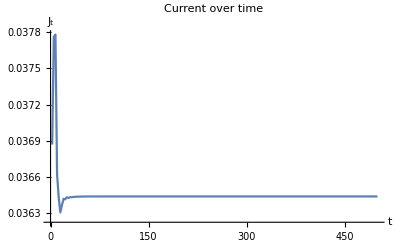
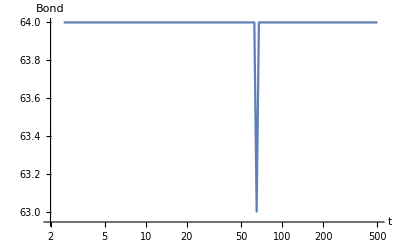
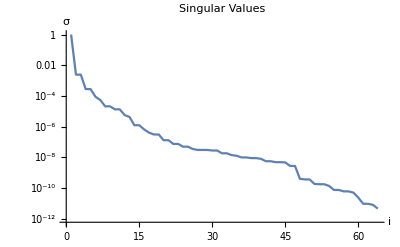
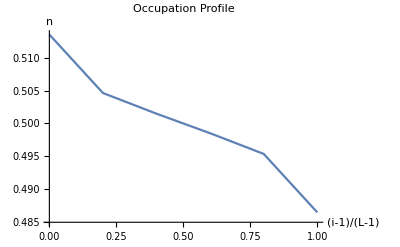
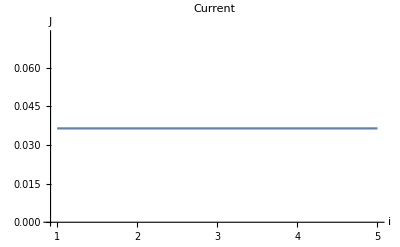
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
XXZPlots[6,64,-0.5,0.25,0.0,0.0,0.1,1.0]
```